```mathematica
anzahlInput = 4; anzahlHidden = 20; anzahlOutput = 1;
l = 4; (*Anzahl Sektoren*)
modulo[z_] := Exp[I Mod[Arg[z],2 Pi/l]];
toComplex[x_] := Exp[I 2 Pi /l x];
toReal[z_] := Arg[z] / (2 Pi/l);
rund[z_] := z /modulo[z];
Activ[z_] := toReal[modulo[z]];
```

```mathematica
weights1 = Table[N[Exp[I   RandomInteger[{1,256}]/256]],{anzahlHidden},{anzahlInput}]
weights2 = Table[N[Exp[I   RandomInteger[{1,256}]/256]],{anzahlOutput},{anzahlHidden}]
```

{{0.667579+0.744539 ⅈ,0.782656+0.622455 ⅈ,0.729021+0.684492 ⅈ,0.75775+0.652544 ⅈ},{0.607435+0.794369 ⅈ,0.762825+0.646605 ⅈ,0.941497+0.33702 ⅈ,0.556633+0.830758 ⅈ},{0.945382+0.325964 ⅈ,0.999809+0.01953 ⅈ,0.556633+0.830758 ⅈ,0.655865+0.754878 ⅈ},{0.622833+0.782355 ⅈ,0.915494+0.402332 ⅈ,0.734346+0.678775 ⅈ,0.945382+0.325964 ⅈ},{0.9479+0.318568 ⅈ,0.924671+0.380766 ⅈ,0.99631+0.0858318 ⅈ,0.676258+0.736665 ⅈ},{0.999725+0.0234354 ⅈ,0.56633+0.824178 ⅈ,0.687686+0.726009 ⅈ,0.664666+0.747141 ⅈ},{0.975314+0.220821 ⅈ,0.715513+0.698599 ⅈ,0.985266+0.17103 ⅈ,0.54686+0.837224 ⅈ},{0.941497+0.33702 ⅈ,0.912323+0.409472 ⅈ,0.999809+0.01953 ⅈ,0.594949+0.803763 ⅈ},{0.999077+0.0429555 ⅈ,0.900787+0.434262 ⅈ,0.998902+0.0468578 ⅈ,0.97701+0.213195 ⅈ},{0.886778+0.462195 ⅈ,0.58549+0.81068 ⅈ,0.970816+0.239827 ⅈ,0.579138+0.815229 ⅈ},{0.994443+0.105273 ⅈ,0.987818+0.155615 ⅈ,0.933341+0.358992 ⅈ,0.983194+0.182564 ⅈ},{0.983194+0.182564 ⅈ,0.958512+0.285054 ⅈ,0.892134+0.451771 ⅈ,0.994443+0.105273 ⅈ},{0.900787+0.434262 ⅈ,0.777769+0.62855 ⅈ,0.731689+0.681639 ⅈ,0.97266+0.232235 ⅈ},{0.99631+0.0858318 ⅈ,0.607435+0.794369 ⅈ,0.938836+0.344365 ⅈ,0.997796+0.0663575 ⅈ},{0.956255+0.292533 ⅈ,0.890362+0.455253 ⅈ,0.969871+0.243617 ⅈ,0.946648+0.322269 ⅈ},{0.808671+0.588261 ⅈ,0.820006+0.572355 ⅈ,0.747462+0.664304 ⅈ,0.701733+0.71244 ⅈ},{0.964929+0.262512 ⅈ,0.673375+0.739301 ⅈ,0.987202+0.159472 ⅈ,0.907462+0.420135 ⅈ},{0.658808+0.752311 ⅈ,0.610533+0.791991 ⅈ,0.729021+0.684492 ⅈ,0.998284+0.0585602 ⅈ},{0.74225+0.670123 ⅈ,0.868052+0.496473 ⅈ,0.991703+0.12855 ⅈ,0.715513+0.698599 ⅈ},{0.64399+0.765034 ⅈ,0.998048+0.0624593 ⅈ,0.892134+0.451771 ⅈ,0.890362+0.455253 ⅈ}}

{{0.926152+0.377152 ⅈ,0.893892+0.448283 ⅈ,0.575949+0.817485 ⅈ,0.607435+0.794369 ⅈ,0.813242+0.581925 ⅈ,0.673375+0.739301 ⅈ,0.999725+0.0234354 ⅈ,0.912323+0.409472 ⅈ,0.801722+0.597697 ⅈ,0.917059+0.398753 ⅈ,0.909096+0.416587 ⅈ,0.628926+0.777465 ⅈ,0.977835+0.209377 ⅈ,0.868052+0.496473 ⅈ,0.720949+0.692988 ⅈ,0.998711+0.0507594 ⅈ,0.868052+0.496473 ⅈ,0.845924+0.533303 ⅈ,0.895636+0.444788 ⅈ,0.99695+0.0780456 ⅈ}}

```mathematica
in= {{0.1,0.1,0.9,0.9},{0.1,0.9,0.9,0.9},{0.9,0.1,0.9,0.9},{0.9,0.9,0.9,0.9}};
in = toComplex[in]
```

{{0.987688+0.156434 ⅈ,0.987688+0.156434 ⅈ,0.156434+0.987688 ⅈ,0.156434+0.987688 ⅈ},{0.987688+0.156434 ⅈ,0.156434+0.987688 ⅈ,0.156434+0.987688 ⅈ,0.156434+0.987688 ⅈ},{0.156434+0.987688 ⅈ,0.987688+0.156434 ⅈ,0.156434+0.987688 ⅈ,0.156434+0.987688 ⅈ},{0.156434+0.987688 ⅈ,0.156434+0.987688 ⅈ,0.156434+0.987688 ⅈ,0.156434+0.987688 ⅈ}}

```mathematica
out= {{0.1},{0.9},{0.9},{0.9}};
out = toComplex[out]
```

{{0.987688+0.156434 ⅈ},{0.156434+0.987688 ⅈ},{0.156434+0.987688 ⅈ},{0.156434+0.987688 ⅈ}}

```mathematica
calcError[] := Module[{err},
err=Transpose[toReal[out]]-calcOutput[];
	1/2*(err.Transpose[err])[[1,1]]];
calcOutput[] :=  Module[{wsum1,wsum2},
wsum1 = weights1.Transpose[in];
wsum2 = weights2.wsum1;
Activ[wsum2]];
```

```mathematica
(*Trainiere Perzeptron*)
```

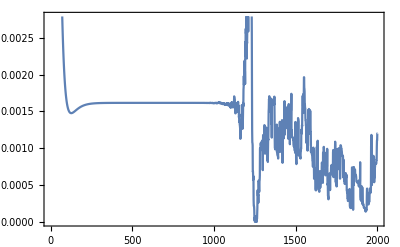

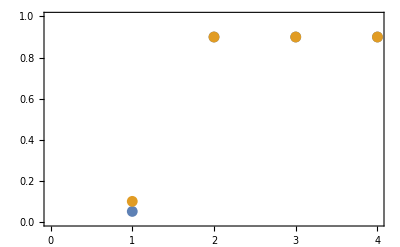

{{0.0509775,0.9,0.9,0.9}}

{{0.1,0.9,0.9,0.9}}

{{0.0490225,0.,4.44089×10^-16,-1.11022×10^-16}}

{-1.93058×10^-8-1.16825×10^-8 ⅈ}

```mathematica
Fehlerliste=Table[
(*Lerne*)
Do[
eta=1;
wsum1 =1/(anzahlInput+1)weights1.in[[i]];
wsum2 =1/(anzahlHidden+1) weights2.wsum1;
soll=out[[i]]*rund[wsum2];
error2=eta(soll-wsum2);
error1 = ConjugateTranspose[weights2].error2;
	diff2=Outer[Times, error2,Conjugate[wsum1]];
	diff1=Outer[Times,error1,Conjugate[in[[i]]]];
	weights2+=diff2;
	weights1+=diff1;
,{i,1,4}];
(*Berechne Error*)
calcError[]
,{epoche,0,2000}];
ListPlot[Fehlerliste,Frame->True,Joined->True](*Printe error*)
(*Schaue ob funktioniert*)
result=calcOutput[];
should=Table[toReal[out[[i]]],{i,4}];
should=Transpose[should];
ListPlot[{result[[1]],should[[1]]},Frame->True,PlotRange->{0,1}]
result
should
should-result
```